```mathematica
f[x_]:=Log[x]
```

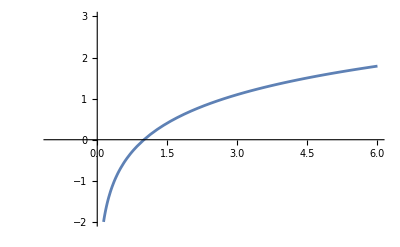

```mathematica
Plot[f[x],{x,-1,6},PlotRange->{{-1,6},{-2,3}}]
```

```mathematica
g[x_]:=x-1
```

```mathematica
h[x_]:=x/E
```

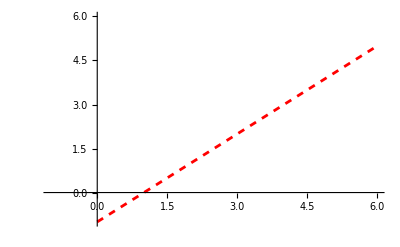

```mathematica
Plot[g[x], {x, -1, 6}, PlotRange -> {-1,6}, PlotStyle -> {Red, Dashed}]
```

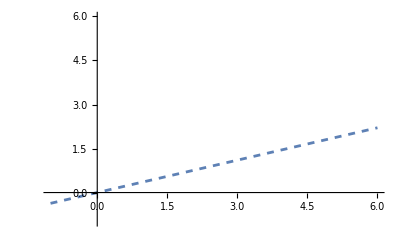

```mathematica
Plot[h[x], {x,-1,6}, PlotRange -> {-1,6}, PlotStyle -> {Grey, Dashed}]
```

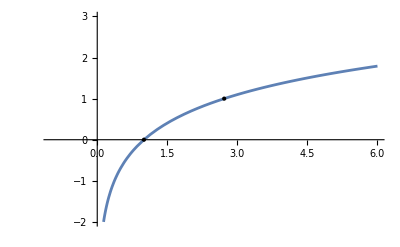

```mathematica
Show[Plot[f[x],{x,-1,6},PlotRange->{{-1,6},{-2,3}}],Graphics[{PointSize[Large],Point[{1,0}],Point[{E,Log[E]}]}]]
```

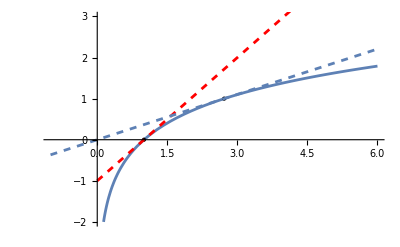

```mathematica
Show[Plot[f[x],{x,-1,6},PlotRange->{{-1,6},{-2,3}}],Graphics[{PointSize[Large],Point[{1,0}],Point[{E,Log[E]}]}],Plot[g[x],{x,-1,6},PlotRange->{-1,6},PlotStyle->{Red,Dashed}],Plot[h[x],{x,-1,6},PlotRange->{-1,6},PlotStyle->{Grey,Dashed}]]
```